# Pchem Assignment 5 – 7 November 2016

```mathematica
tdnatall = Transpose[Import[ "/Users/mlnance/JHU_Class_Material/pchem/assignment_5/TDenat.xlsx","Data"]]
tdnat=Transpose[tdnatall[[2;;]]][[1]];
```

{{{Temperature,Fluorescence}},{{20.,384827.}},{{24.,378109.}},{{28.,368302.}},{{32.,351668.}},{{36.,337514.}},{{40.,313397.}},{{44.,268746.}},{{48.,178369.}},{{52.,81084.4}},{{56.,46140.6}},{{60.,36678.5}},{{64.,33935.7}},{{68.,29980.3}},{{72.,28432.7}}}

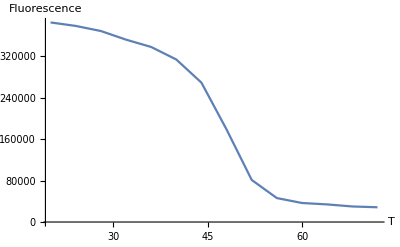

```mathematica
(*Plot the denaturation data*)
ListLinePlot[tdnat,PlotRange->All,AxesLabel->{"T","Fluorescence"}]
```

```mathematica
(*Fit the denaturation data to an equation*)
(*nlm=NonLinearModelFit[tdnat,ka*x/(1+(ka*x)),ka,x]*)
```